## Basic usage examples

### Importing the package and generating the matrices

In this notebook basic usage of the library is demonstrated. After importing the library

```mathematica
Needs["SUN`"]
```

we can initialize an irreducible representation:

```mathematica
rep = Irrep[1,0]
```

Irrep[…]

This is just a summary box, representing the irreducible representation and does not hold the matrix data yet. It gives however a brief overview of the irreducible representation. To construct the matrices, we can proceed by evaluating

```mathematica
m = LieAlgebraBasisMatrices[rep]
```

IrrepBasis[…]

This generates a set of basis matrices that can be accessed by

```mathematica
MatrixForm[m[1]]
```

(0 | 1/2 | 0
1/2 | 0 | 0
0 | 0 | 0)

The arguments can be anything that can be passed to arrays as well. For example, we can retrieve a list of all matrices with the All identifier, like so for example

```mathematica
MatrixForm/@m[All]
```

{(0 | 1/2 | 0
1/2 | 0 | 0
0 | 0 | 0),(0 | ⅈ/2 | 0
-ⅈ/2 | 0 | 0
0 | 0 | 0),(0 | 0 | 1/2
0 | 0 | 0
1/2 | 0 | 0),(0 | 0 | ⅈ/2
0 | 0 | 0
-ⅈ/2 | 0 | 0),(0 | 0 | 0
0 | 0 | 1/2
0 | 1/2 | 0),(0 | 0 | 0
0 | 0 | ⅈ/2
0 | -ⅈ/2 | 0),(1/2 | 0 | 0
0 | -1/2 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 1/2 | 0
0 | 0 | -1/2)}

### Weight lattice for 𝔰𝔲(3) and 𝔰𝔲(4)

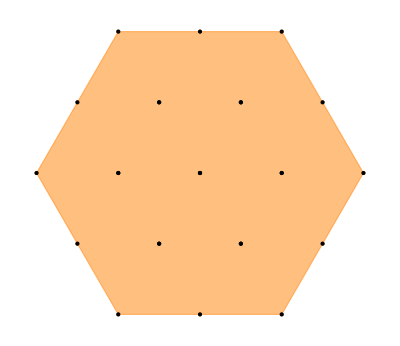

```mathematica
x=SU3BasisMatrices[2,2][{3,8}];

Show[
ConvexHullMesh[Transpose@Normal[Diagonal/@x],
MeshCellStyle->{All->{Orange,Opacity[0.5]}}],
Graphics[{PointSize[Large],Point/@Transpose@Normal[Diagonal/@x]}]
]
```

```mathematica
x=LieAlgebraBasisMatrices[Irrep[2,2,2]][{13,14,15}];
x=SparseArray[Transpose@{Range@Length[#],Range@Length[#]}->#]&/@Orthogonalize[Diagonal/@x];

Show[
ConvexHullMesh[Transpose@Normal[Diagonal/@x],
MeshCellStyle->{{2,All}->{Orange,Opacity[0.5]}}],
Graphics3D[{PointSize[Large],Point/@Transpose@Normal[Diagonal/@x]}],
ViewPoint->{10000,10000,10000}
]
```

-Graphics3D-